```mathematica
(*Compute the repo root from the notebook location*)repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## Nodal Curve Parametrization

```mathematica
F1=MirrorCurveLocalF1[x,y,m,u]
```

-1/u+m/x+x+1/(x y)+y

```mathematica
m1=WeierstrassChangeOfVariables[{x,y}->{X,Y},m,u]
```

{x→(-9+36 u^2 (m+3 u)+6 X+√2 Y)/(6 u (-3+12 m u^2+2 X)),y→(36 u^2)/(3-12 m u^2-2 X)}

```mathematica
m2=WeierstrassChangeOfVariablesInverse[{X,Y}->{x,y},m,u]
```

{X→3/2-(6 u^2 (3+m y))/y,Y→-(54 √2 u^2 (-1+u (2 x+y)))/y}

```mathematica
Simplify[{x,y}/.m1/.m2]
```

{x,y}

```mathematica
Simplify[{X,Y}/.m2/.m1]
```

{X,Y}

```mathematica
Simplify[F1/.m1]
Numerator[%]
Simplify@Flatten[{Coefficient[%, {Y^2, X^4, X^3, X^2, X}], (%/.{X->0,Y->0}), -%/.Y->0}]//TableForm
```

(-27-5832 u^6+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-4 X^3-324 u^3 (-3+2 X)-108 m u^2 (-3+36 u^3+2 X)+Y^2)/(3 u (-3+12 m u^2+2 X) (-9+36 m u^2+108 u^3+6 X+√2 Y))

-27-5832 u^6+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-4 X^3-324 u^3 (-3+2 X)-108 m u^2 (-3+36 u^3+2 X)+Y^2

1
0
-4
0
27 (1-8 m u^2-24 u^3+16 m^2 u^4)
27 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6)
5832 u^6-1728 m^3 u^6-432 m^2 u^4 (-3+X)+(3-2 X)^2 (3+X)+324 u^3 (-3+2 X)+108 m u^2 (-3+36 u^3+2 X)

```mathematica
{MirrorCurveg2[m,u],MirrorCurveg3[m,u],MirrorCurvef3[X,m,u]}//TableForm
```

27 (1-8 m u^2-24 u^3+16 m^2 u^4)
27 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6)
5832 u^6-1728 m^3 u^6-432 m^2 u^4 (-3+X)+(3-2 X)^2 (3+X)+324 u^3 (-3+2 X)+108 m u^2 (-3+36 u^3+2 X)

```mathematica
Simplify[1/(544195584 u^8)Discriminant[MirrorCurvef3[X,m,u], X]]
MirrorCurveDelta[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
ClearAll[uvals];
uvals[m_]:=SortBy[Solve[delt[m,u]==0,u], Abs[u/.#]&];
```

```mathematica
(* for m=0, possible values of u *)
Solve[MirrorCurveDelta[0,u]==0,u]
```

{{u→0},{u→1/3},{u→-1/3 (-1)^(1/3)},{u→1/3 (-1)^(2/3)}}

```mathematica
(* for m=1, possible values of u *)
Solve[MirrorCurveDelta[1.,u]==0,u]
```

{{u→-3.02572},{u→-0.255099-0.221553 ⅈ},{u→-0.255099+0.221553 ⅈ},{u→0.263185}}

```mathematica
4(X-X0)^2(X+2X0)//Expand
Y^2-%/.{X->t^2-2X0, Y->2t(t^2-3X0)}//Simplify
```

4 X^3-12 X X0^2+8 X0^3

0

```mathematica
p1 = {X->t^2-2X0, Y->2t(t^2-3X0)};
p1 = p1/.{t->t/Sqrt[2]}//Simplify
Y^2-4(X-X0)^2(X+2X0)/.p1//Simplify
```

{X→1/2 (t^2-4 X0),Y→(t (t^2-6 X0))/(√2)}

0

```mathematica
First@Solve[Simplify[-12 X0^2/(8 X0^3)]==(-G2/-G3), X0]
```

{X0→-(3 G3)/(2 G2)}

```mathematica
-(3 MirrorCurveg3[m,u])/(2 MirrorCurveg2[m,u])//FullSimplify
```

(3+12 u^2 (-3 m-9 u+12 m^2 u^2+36 m u^3+2 (27-8 m^3) u^4))/(2+16 u^2 (-3 u+m (-1+2 m u^2)))

```mathematica
First@Solve[Simplify[-12 X0^2/(8 X0^3)]==(-MirrorCurveg2[m,u]/-MirrorCurveg3[m,u]), X0]
X0sol = FullSimplify[%, MirrorCurveDelta[m,u]==0]//Together
```

{X0→-(3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

{X0→(3 (1-8 m u^2-32 u^3+16 m^2 u^4+108 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

```mathematica
X0tot1={X0->-3/4+t1^2/4+3 m u^2};
```

```mathematica
{x, y}/.m1/.p1
pxy = %/.X0tot1//Simplify
```

{(-9+36 u^2 (m+3 u)+t (t^2-6 X0)+3 (t^2-4 X0))/(6 u (-3+t^2+12 m u^2-4 X0)),(36 u^2)/(3-t^2-12 m u^2+4 X0)}

{(9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3)/(12 t^2 u-12 t1^2 u),-(36 u^2)/(t^2-t1^2)}

```mathematica
sol = FullSimplify[Solve[{(X0/.X0tot1)==(X0/.X0sol), delt[m,u]==0}, {m, u}]];
```

```mathematica
sol[[2]]
```

{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→(t1^(2/3) (3+t1)^(1/3))/(3 2^(1/3))}

```mathematica
9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3
FullSimplify[%/.sol[[2]]]
pxy1 = pxy/.{9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3->%}//Simplify
```

9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3

2 (t-t1)^2 (3+t+2 t1)

{((t-t1) (3+t+2 t1))/(6 (t+t1) u),-(36 u^2)/(t^2-t1^2)}

```mathematica
FullSimplify[X0sol/.sol[[2]]]
```

{X0→1/2 t1 (2+t1)}

```mathematica
-2+Sqrt[1+12m u^2]/.sol[[2]]//Simplify//PowerExpand
```

t1

```mathematica
t1s = 3(4m u^2+18u^3-1)/(1+12m u^2);
t1s/.sol[[2]]//Simplify
```

t1

```mathematica
X0s = (-3+12m u^2)/2-t1s//Simplify
```

(3 (1-16 m u^2-36 u^3+48 m^2 u^4))/(2+24 m u^2)

```mathematica
t/.Solve[X0==(X/.p1), t]
Solve[z==(t-%[[2]])/(t-%[[1]]), t]//Simplify
pxy2 = Together[pxy1/.First[%]]
```

{-√6 √X0,√6 √X0}

{{t→-(√6 √X0 (1+z))/(-1+z)}}

{-((-3-2 t1-√6 √X0+3 z+2 t1 z-√6 √X0 z) (-t1+√6 √X0+t1 z+√6 √X0 z))/(6 u (-1+z) (-t1-√6 √X0+t1 z-√6 √X0 z)),(36 u^2 (-1+z)^2)/(t1^2-6 X0-2 t1^2 z-12 X0 z+t1^2 z^2-6 X0 z^2)}

```mathematica
pxy2/.{X0->1/2t1^2+t1}
```

{-(((-3-2 t1-√6 √(t1+t1^2/2)+3 z+2 t1 z-√6 √(t1+t1^2/2) z) (-t1+√6 √(t1+t1^2/2)+t1 z+√6 √(t1+t1^2/2) z))/(6 u (-1+z) (-t1-√6 √(t1+t1^2/2)+t1 z-√6 √(t1+t1^2/2) z))),(36 u^2 (-1+z)^2)/(t1^2-6 (t1+t1^2/2)-2 t1^2 z-12 (t1+t1^2/2) z+t1^2 z^2-6 (t1+t1^2/2) z^2)}

```mathematica
Limit[pxy2, z->Infinity]/.sol[[2]]/.{X0->1/2t1^2+t1}//FullSimplify
```

{1/(2^(2/3) (t1/(3+t1))^(2/3)),-2^(1/3) (t1/(3+t1))^(1/3)}

```mathematica
Limit[pxy2, z->Infinity]//FullSimplify
%/.{X0->1/2t1^2+t1}//FullSimplify
%/.{t1->-2+Sqrt[1+12m u^2]}//Simplify
```

{-(3 t1+2 t1^2+3 √6 √X0+√6 t1 √X0-6 X0)/(6 t1 u-6 √6 u √X0),(36 u^2)/(t1^2-6 X0)}

{(3+t1)/(6 u),-(18 u^2)/(3 t1+t1^2)}

{(1+√(1+12 m u^2))/(6 u),(18 u^2)/(1-12 m u^2+√(1+12 m u^2))}

```mathematica
{dvec,avec} = RationalData[pxy2[[1]], z]
{evec, bvec} = RationalData[Factor[pxy2[[2]]/.{X0->x0sqrt^2},Extension->{Sqrt[6]}], z]/.{x0sqrt->Sqrt[X0]}
```

{{1,1,-1,-1},{(3+2 t1+√6 √X0)/(3+2 t1-√6 √X0),(t1-√6 √X0)/(t1+√6 √X0),1,(t1+√6 √X0)/(t1-√6 √X0)}}

{{2,-1,-1},{1,(t1+√6 √X0)/(t1-√6 √X0),(t1-√6 √X0)/(t1+√6 √X0)}}

```mathematica
(3+2 t1+√6 √X0)/(3+2 t1-√6 √X0)((t1-√6 √X0)/(t1+√6 √X0))^2
%/.{X0->1/2t1^2+t1}//Simplify
```

((t1-√6 √X0)^2 (3+2 t1+√6 √X0))/((3+2 t1-√6 √X0) (t1+√6 √X0)^2)

1

#### Can we write α β in terms of b

```mathematica
bTot1={b->(t1-√6 √X0)/(t1+√6 √X0)};
```

```mathematica
(t1-√6 √X0)/(t1+√6 √X0)/.{X0->t1^2/2+t1}//FullSimplify
%/.{√(t1 (2+t1))->sq}
t1 (2+t1)-sq^2/.First@Solve[b==%, sq]//Expand//FullSimplify
Solve[%==0, t1]
```

(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)

(-3+√3 sq-2 t1)/(3+t1)

-1/3 (3+t1) (3 (1+b)^2+t1+b (4+b) t1)

{{t1→-3},{t1→-(3 (1+2 b+b^2))/(1+4 b+b^2)}}

```mathematica
{(3+t1)/(6 u),-(18 u^2)/(3 t1+t1^2)}/.sol2[[1]]//Simplify
Assuming[b>1, Simplify[%/.{t1->-(3 (1+2 b+b^2))/(1+4 b+b^2)}]]
```

{(-1/2)^(2/3)/(t1/(3+t1))^(2/3),-(-1)^(2/3) 2^(1/3) (t1/(3+t1))^(1/3)}

{1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)}

```mathematica
(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)/.{t1->-2+Sqrt[1+12m u^2]}
FullSimplify[%, MirrorCurveDelta[m,u]==0]
```

(-3-2 (-2+√(1+12 m u^2))+√3 √(√(1+12 m u^2) (-2+√(1+12 m u^2))))/(1+√(1+12 m u^2))

(1-2 √(1+12 m u^2)+√(3+36 m u^2-6 √(1+12 m u^2)))/(1+√(1+12 m u^2))

## Kerr Doran: Imaginary part of period

```mathematica
{dvec,avec}={{1,1,-1,-1},{1/b^2,b,1,1/b}};
{evec,bvec}={{2,-1,-1},{1,1/b,b}};
```

```mathematica
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
```

-(BW[1/b^3]-3 BW[1/b^2]+2 BW[1/b]-3 BW[b]+BW[b^2])/(2 π)

```mathematica
BWRules = {{BW[z_]:>BW[1-1/z]}, {BW[z_]:>BW[1/(1-z)]}, {BW[z_]:>-BW[1/z]}, {BW[z_]:>-BW[1-z]}, {BW[z_]:>-BW[-z/(1-z)]}};
BWFiveTerm[x_,y_] := BW[x] + BW[y] + BW[(1-x)/(1-x y)] + BW[1-x y] + BW[(1-y)/(1-x y)];
BWEval={BW[x_]:>Im[PolyLog[2, x]]+Arg[1-x]Log[Abs[x]]};
```

```mathematica
Cases[A, BW[__], Infinity]
```

{BW[1/b^3],BW[1/b^2],BW[1/b],BW[b],BW[b^2]}

```mathematica
BW[1/b^n]/.BWRules
```

{BW[1-b^n],BW[1/(1-b^-n)],-BW[b^n],-BW[1-b^-n],-BW[-b^-n/(1-b^-n)]}

```mathematica
A1 = A/.{BW[1/b]->-BW[b],BW[1/b^2]->-BW[b^2], BW[1/b^3]->-BW[b^3]}//Simplify
```

(5 BW[b]-4 BW[b^2]+BW[b^3])/(2 π)

## Kerr Doran: Full period

```mathematica
{dvec,avec}={{1,1,-1,-1},{1/b^2,b,1,1/b}};
{evec,bvec}={{2,-1,-1},{1,1/b,b}};
{Xat0,wat0} = {1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)};
XatInf=Xat0;
```

```mathematica
b0 = 1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

b1 = -1/2/Pi Log[wat0](Log[Xat0]-Log[XatInf])//Simplify;

b2 = 1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

b3 = -1/2/Pi Log[XatInf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = b0 + b1 + b2 + b3//Simplify
```

1/(6 π)(3 (Log[1/b]+Log[b]) Log[1/(2+1/b+b)^(2/3)]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[2+1/b+b]-3 (Li2[1/b^3]-Li2[1/b^2]-Li2[b]+Li2[b^2]-2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])+Log[1-b] Log[1/b]+(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]+2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])+Log[1-1/b^3] (Log[1/b^2]-Log[b])-Log[1-1/b^2] (Log[1/b]-Log[b])+Log[(-1+b)/b] Log[b]-2 (Li2[b]+Log[1-b] Log[b])-(Log[1/b]-Log[b]) Log[1-b^2]))

```mathematica
Li2Rules = {{Li2[z_]:>-Li2[1/z]-Pi^2/6-1/2 Log[-1/z]^2}, {Li2[z_]:>-Li2[1-z]+Pi^2/6-Log[z]Log[1-z]}};
```

```mathematica
Li2FiveTerm[x_, y_] = Simplify[L[x]+L[y]+L[1-x y]+L[(1-x)/(1-x y)]+L[(1-y)/(1-x y)]-3Pi^2/6/.{L[z_]:>Li2[z]+1/2Log[z]Log[1-z]}];
```

```mathematica
Li2Eval = {Li2[z_]:>PolyLog[2, z]};
```

```mathematica
Cases[B,Li2[_],Infinity]//DeleteDuplicates
```

{Li2[1/b^3],Li2[1/b^2],Li2[b],Li2[b^2],Li2[1/b]}

```mathematica
Li2[1/b^3]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2),1/6 (π^2-6 Li2[1-1/b^3]-6 Log[1-1/b^3] Log[1/b^3])}

```mathematica
Li2[1/b^2]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),1/6 (π^2-6 Li2[1-1/b^2]-6 Log[1-1/b^2] Log[1/b^2])}

```mathematica
Li2[1/b]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b]-3 Log[-b]^2),1/6 (π^2-6 Li2[(-1+b)/b]-6 Log[1/b] Log[(-1+b)/b])}

```mathematica
rules={
Li2[1/b^3]->1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2),
Li2[1/b^2]->1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),
Li2[1/b]->1/6 (-π^2-6 Li2[b]-3 Log[-b]^2)
};
temp = B/.rules/.{Li2[_]:>0}//Simplify
```

1/(12 π)(-6 Log[1-b] Log[1/b]-6 Log[1/b^2] Log[(-1+b)/b]-6 Log[1/b] Log[(-1+b)/b]+6 Log[-b]^2-6 Log[1-1/b^3] (Log[1/b^2]-Log[b])+6 Log[1-1/b^2] (2 Log[1/b^2]+Log[1/b]-Log[b])+12 Log[1-b] Log[b]-6 Log[(-1+b)/b] Log[b]-9 Log[-b^2]^2+3 Log[-b^3]^2+6 Log[1/b] Log[1/(2+1/b+b)^(2/3)]+6 Log[b] Log[1/(2+1/b+b)^(2/3)]+2 Log[1/b^2] Log[2+1/b+b]-2 Log[1/b] Log[2+1/b+b]+2 Log[b] Log[2+1/b+b]+6 Log[1/b] Log[1-b^2]-6 Log[b] Log[1-b^2])

```mathematica
-1+b^3//Factor
```

(-1+b) (1+b+b^2)

```mathematica
12Pi temp/2/3//Expand
%/.{Log[x_/y_]:>Log[x]-Log[y]}/.{Log[x_*y_]:>Log[x]+Log[y]}/.{Log[b^n_]:>n Log[b]}
Map[Together, %, Infinity]/.{Log[x_/y_]:>Log[x]-Log[y]}/.{Log[x_*y_]:>Log[x]+Log[y]}/.{Log[b^n_]:>n Log[b]}
%/.{Log[1-b^2]->Log[1-b]+Log[1+b], Log[-1+b^2]->Log[b-1]+Log[1+b],Log[-1+b^3]->Log[b-1]+Log[1+b+b^2]}//ExpandAll//Simplify
temp2 = %/.{-2 ⅈ π+2 Log[1-b]-2 Log[-1+b]->-4 ⅈ π}
```

-Log[1-1/b^3] Log[1/b^2]+2 Log[1-1/b^2] Log[1/b^2]+Log[1-1/b^2] Log[1/b]-Log[1-b] Log[1/b]-Log[1/b^2] Log[(-1+b)/b]-Log[1/b] Log[(-1+b)/b]+Log[-b]^2+Log[1-1/b^3] Log[b]-Log[1-1/b^2] Log[b]+2 Log[1-b] Log[b]-Log[(-1+b)/b] Log[b]-3/2 Log[-b^2]^2+1/2 Log[-b^3]^2+Log[1/b] Log[1/(2+1/b+b)^(2/3)]+Log[b] Log[1/(2+1/b+b)^(2/3)]+1/3 Log[1/b^2] Log[2+1/b+b]-1/3 Log[1/b] Log[2+1/b+b]+1/3 Log[b] Log[2+1/b+b]+Log[1/b] Log[1-b^2]-Log[b] Log[1-b^2]

3 Log[1-1/b^3] Log[b]-6 Log[1-1/b^2] Log[b]+3 Log[1-b] Log[b]+2 (Log[-1+b]-Log[b]) Log[b]+(ⅈ π+Log[b])^2-3/2 (ⅈ π+2 Log[b])^2+1/2 (ⅈ π+3 Log[b])^2-2 Log[b] Log[1-b^2]

-(π-ⅈ Log[b])^2+3/2 (π-2 ⅈ Log[b])^2-1/2 (π-3 ⅈ Log[b])^2+3 Log[1-b] Log[b]+2 (Log[-1+b]-Log[b]) Log[b]-2 Log[b] Log[1-b^2]-6 Log[b] (-2 Log[b]+Log[-1+b^2])+3 Log[b] (-3 Log[b]+Log[-1+b^3])

1/2 Log[b] (-2 ⅈ π+2 Log[1-b]-2 Log[-1+b]+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

1/2 Log[b] (-4 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

```mathematica
FullSimplify[-2 ⅈ π+2 Log[1-b]-2 Log[-1+b], Im[b]>0]
```

-4 ⅈ π

```mathematica
Together[(B/.rules)-temp]+temp2/2/Pi
%/.{b->-0.7251497610490148665275651524636838940601276942612714222276`38.51933138562852+0.6885911878978387285805195905580644422553067984717644767418`38.67353511270891 ⅈ}/.Li2Eval
```

(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (-4 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4 π)

6.047239614429887673081434793311933591+1.157322100746665312432350757333190625 ⅈ

```mathematica
(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (+5I Pi+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4π)
%/.{b->-0.7251497610490148665275651524636838940601276942612714222276`38.51933138562852+0.6885911878978387285805195905580644422553067984717644767418`38.67353511270891 ⅈ}/.Li2Eval
```

(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (5 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4 π)

0.687631197635847659612645389468778082+1.157322100746665312432350757333190625 ⅈ

## From first principles

```mathematica
fanGen={{0,0},{1,0},{-1,-1},{-1,0},{0,1}};
```

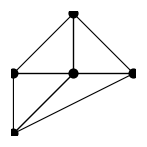

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],Polygon@Take[fanGen,-4], Line/@Thread[{Take[fanGen,-4], First[fanGen]}, List, 1], PointSize[.05],Point@fanGen}]
```

```mathematica
fanV = ArrayPad[fanGen, {{0,0}, {0,1}}, 1]
```

{{0,0,1},{1,0,1},{-1,-1,1},{-1,0,1},{0,1,1}}

```mathematica
Solve[Thread[fanVᵀ.Array[a,5]==0], Array[a,5], Integers]
fanQ = Array[a,5]/.First[%]/.{{C[1]->-2,C[2]->1},{C[1]->-1,C[2]->0}}
fanVQ = Join[fanVᵀ, %]ᵀ;
fanVQ//MatrixForm
```

{{a[1]→ConditionalExpression[C[1], (C[1]|C[2])∈ℤ],a[2]→ConditionalExpression[C[2], (C[1]|C[2])∈ℤ],a[3]→ConditionalExpression[-C[1]-2 C[2], (C[1]|C[2])∈ℤ],a[4]→ConditionalExpression[C[1]+3 C[2], (C[1]|C[2])∈ℤ],a[5]→ConditionalExpression[-C[1]-2 C[2], (C[1]|C[2])∈ℤ]}}

{{-2,1,0,1,0},{-1,0,1,-1,1}}

(0 | 0 | 1 | -2 | -1
1 | 0 | 1 | 1 | 0
-1 | -1 | 1 | 0 | 1
-1 | 0 | 1 | 1 | -1
0 | 1 | 1 | 0 | 1)

```mathematica
CSMDef = Thread[Array[z,Length[fanQ]]->Table[Product[a[i]^fanQ[[A, i]], {i,1,5}], {A, 1, Length[fanQ]}]]
```

{z[1]→(a[2] a[4])/a[1]^2,z[2]→(a[3] a[5])/(a[1] a[4])}

```mathematica
H[X_,Y_]=Sum[a[i]X^fanVQ[[i,1]]Y^fanVQ[[i,2]], {i,Length[fanVQ]}]
```

a[1]+X a[2]+a[3]/(X Y)+a[4]/X+Y a[5]

```mathematica
H[X,Y]/a[1]/.{X->xc X, Y->yc Y}//Expand
H1[X_,Y_]=%/.{xc->a[1]/a[2], yc->a[1]/a[5]}/.{(a[2] a[4])/a[1]^2->z[1],(a[3] a[5])/(a[1] a[4])->z[2]}/.{(a[2] a[3] a[5])/a[1]^3->z[1]z[2]}
```

1+(X xc a[2])/a[1]+a[3]/(X xc Y yc a[1])+a[4]/(X xc a[1])+(Y yc a[5])/a[1]

1+X+Y+z[1]/X+(z[1] z[2])/(X Y)

## Periods from gamma soln

```mathematica
Gamma/@(fanQᵀ.{n1+r1,n2+r2}+1)
expr1 = z1^(n1+r1) z2^(n2+r2)/Times@@%
expr2 = %/.{Gamma[1-n2-2 (n1+r1)-r2]->Pi (n2+2 (n1+r1)+r2)/Sin[Pi (n2+2 (n1+r1)+r2)]/Gamma[1+n2+2 (n1+r1)+r2]}
```

{Gamma[1-n2-2 (n1+r1)-r2],Gamma[1+n1+r1],Gamma[1+n2+r2],Gamma[1+n1-n2+r1-r2],Gamma[1+n2+r2]}

(z1^(n1+r1) z2^(n2+r2))/(Gamma[1+n1+r1] Gamma[1+n1-n2+r1-r2] Gamma[1-n2-2 (n1+r1)-r2] Gamma[1+n2+r2]^2)

(z1^(n1+r1) z2^(n2+r2) Gamma[1+n2+2 (n1+r1)+r2] Sin[π (n2+2 (n1+r1)+r2)])/(π (n2+2 (n1+r1)+r2) Gamma[1+n1+r1] Gamma[1+n1-n2+r1-r2] Gamma[1+n2+r2]^2)

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Limit[%, {n1,n2}->{0,0}]
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z1]

```mathematica
Simplify[D[expr2, r1]/.{r1->0,r2->0}]
Limit[%, {n1->0,n2->0}]
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (4 n1 π Cos[(2 n1+n2) π]+2 n2 π Cos[(2 n1+n2) π]-2 Sin[(2 n1+n2) π]+2 n1 Log[z1] Sin[(2 n1+n2) π]+n2 Log[z1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+4 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+2 n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z1]

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

0

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

ConditionalExpression[(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2), 2 n1+n2<1]

```mathematica
Simplify[D[expr2, r1]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (4 n1 π Cos[(2 n1+n2) π]+2 n2 π Cos[(2 n1+n2) π]-2 Sin[(2 n1+n2) π]+2 n1 Log[z1] Sin[(2 n1+n2) π]+n2 Log[z1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+4 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+2 n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

(2 z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
vpi1[z1_,z2_,0,0]:=Log[z1];
vpi1[z1_,z2_,n1_Integer,n2_Integer]:=0/;n1<n2;
vpi1[z1_,z2_,n1_Integer,n2_Integer]:=(2 z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)/;n1>=n2;
```

#### t2?

```mathematica
Simplify[D[expr1, r2]/.{r1->0,r2->0}]
Limit[%, {n1,n2}->{0,0}]
```

(z1^n1 z2^n2 (Log[z2]+PolyGamma[0,1-2 n1-n2]+PolyGamma[0,1+n1-n2]-2 PolyGamma[0,1+n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z2]

```mathematica
Simplify[D[expr2, r2]/.{r1->0,r2->0}]
Limit[%, {n1->0,n2->0}]
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (2 n1 π Cos[(2 n1+n2) π]+n2 π Cos[(2 n1+n2) π]-Sin[(2 n1+n2) π]+2 n1 Log[z2] Sin[(2 n1+n2) π]+n2 Log[z2] Sin[(2 n1+n2) π]+(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]-2 (2 n1+n2) PolyGamma[0,1+n2] Sin[(2 n1+n2) π]+2 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z2]

```mathematica
Simplify[D[expr1, r2]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z2]+PolyGamma[0,1-2 n1-n2]+PolyGamma[0,1+n1-n2]-2 PolyGamma[0,1+n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

0

```mathematica
Simplify[D[expr2, r2]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (2 n1 π Cos[(2 n1+n2) π]+n2 π Cos[(2 n1+n2) π]-Sin[(2 n1+n2) π]+2 n1 Log[z2] Sin[(2 n1+n2) π]+n2 Log[z2] Sin[(2 n1+n2) π]+(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]-2 (2 n1+n2) PolyGamma[0,1+n2] Sin[(2 n1+n2) π]+2 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

(z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
vpi2[z1_,z2_,0,0]:=Log[z2];
vpi2[z1_,z2_,n1_Integer,n2_Integer]:=0/;n1<n2;
vpi2[z1_,z2_,n1_Integer,n2_Integer]:=(z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)/;n1>=n2;
```

#### continue

```mathematica
Table[vpi1[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

2 z1+3 z1^2+(20 z1^3)/3-4 z1 z2-24 z1^2 z2-120 z1^3 z2+30 z1^2 z2^2+420 z1^3 z2^2-(1120 z1^3 z2^3)/3+Log[z1]

```mathematica
Table[vpi2[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

z1+(3 z1^2)/2+(10 z1^3)/3-2 z1 z2-12 z1^2 z2-60 z1^3 z2+15 z1^2 z2^2+210 z1^3 z2^2-(560 z1^3 z2^3)/3+Log[z2]

```mathematica
Table[vpi1[z1,z2,n1,n2]-2vpi2[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

Log[z1]-2 Log[z2]

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
FullSimplify[Limit[%, {n1,n2}->{0,0}]]
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

-π^2+Log[z1]^2

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

$Aborted

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,2nn1+nn2>=1,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

-((4 z1^n1 (-z2)^n2 (-1+2 n1+n2)! (2 EulerGamma-2 HarmonicNumber[-1+2 n1+n2]-Log[z1]+PolyGamma[0,1+n1]+PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2))

```mathematica
Simplify[D[expr2, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,2nn1+nn2<1,(nn1|nn2)∈NonNegativeIntegers}, FullSimplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] ((8-4 (2 n1+n2) Log[z1]+(2 n1+n2)^2 Log[z1]^2+2 (2 n1+n2) (2-(2 n1+n2) Log[z1]) PolyGamma[0,1+n1]+(2 n1+n2)^2 (PolyGamma[0,1+n1]^2-PolyGamma[1,1+n1])) Sin[(2 n1+n2) π]+2 (2 n1+n2) (-2+(2 n1+n2) Log[z1]-(2 n1+n2) PolyGamma[0,1+n1]) (2 π Cos[(2 n1+n2) π]-PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π])-(2 n1+n2)^2 (-8 π Cos[(2 n1+n2) π] PolyGamma[0,1+2 n1+n2]-PolyGamma[0,1+n1-n2]^2 Sin[(2 n1+n2) π]-4 PolyGamma[0,1+2 n1+n2]^2 Sin[(2 n1+n2) π]+(4 π^2+PolyGamma[1,1+n1-n2]-4 PolyGamma[1,1+2 n1+n2]) Sin[(2 n1+n2) π]+4 PolyGamma[0,1+n1-n2] (π Cos[(2 n1+n2) π]+PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))))/((2 n1+n2)^3 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
expr3 = FullSimplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
```

(z1^n1 z2^n2 ((HarmonicNumber[n1]-2 HarmonicNumber[-2 n1-n2]+HarmonicNumber[n1-n2]-Log[z1])^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
expr4 = D[expr2, {r1,2}]/.{r1->0,r2->0};
```

```mathematica
Limit[expr4,{n1->0,n2->0}]//FullSimplify
```

-π^2+Log[z1]^2

```mathematica
Table[Simplify[Limit[expr3,{n1->N1,n2->N2}]], {N1,0,3},{N2,0,3}]//MatrixForm
```

(-π^2+Log[z1]^2 | -4 z2 | -z2^2 | -(4 z2^3)/9
4 z1 Log[z1] | -8 z1 z2 (2+Log[z1]) | 6 z1 z2^2 | (8 z1 z2^3)/3
2 z1^2 (2+3 Log[z1]) | -16 z1^2 z2 (5+3 Log[z1]) | 4 z1^2 z2^2 (46+15 Log[z1]) | -40 z1^2 z2^3
4/3 z1^3 (9+10 Log[z1]) | -8 z1^3 z2 (47+30 Log[z1]) | 8 z1^3 z2^2 (247+105 Log[z1]) | -16/9 z1^3 z2^3 (1513+420 Log[z1]))

### Picard Fuchs

```mathematica
FunctionSum
```

```mathematica
PF1[f_,z1_,z2_]:=z1 D[z1 D[f, z1]-z2 D[f, z2], z1]-z1 (2z1 D[f + 2 z1 D[f, z1] + z2 D[f, z2], z1]+z2 D[f + 2 z1 D[f, z1] +  z2 D[f, z2], z2]);
```

```mathematica
PF2[f_,z1_,z2_]:=z2 D[z2 D[f, z2], z2]-z2 (z2 D[2 z1 D[f, z1] + z2 D[f, z2], z2]-z1 D[2 z1 D[f, z1] + z2 D[f, z2], z1]);
```

```mathematica
PF1[z1^2+z2^2,z1,z2]
```

4 z1^2-z1 (20 z1^2+10 z2^2)

```mathematica
Series[Sum[vpi1[z1,z2,n1,n2], {n1,0,10},{n2,0,10}], {z1,0,10},{z2,0,10}];
Simplify[z2 D[%, z2]];
PF1[%,z1,z2]//Simplify
```

O[z1]^11

```mathematica
PF2[z1 D[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z1],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
```

1/27 (4 lam f^(0,1)[ut,lam]+12 lam^2 f^(0,2)[ut,lam]+4 lam^3 f^(0,3)[ut,lam]-ut f^(1,0)[ut,lam]-3 lam ut f^(1,1)[ut,lam]-9 lam f^(1,2)[ut,lam]-3 ut^2 f^(2,0)[ut,lam]+9 ut f^(2,1)[ut,lam]-3 lam ut^2 f^(2,1)[ut,lam]-ut^3 f^(3,0)[ut,lam])

```mathematica
PF1[z2 D[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z2],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
```

1/9 lam (-2 f^(0,1)[ut,lam]-6 lam f^(0,2)[ut,lam]-2 lam^2 f^(0,3)[ut,lam]+2 ut f^(1,1)[ut,lam]+lam ut f^(1,2)[ut,lam]+6 f^(2,0)[ut,lam]+6 lam f^(2,1)[ut,lam]+ut^2 f^(2,1)[ut,lam]+3 ut f^(3,0)[ut,lam])

```mathematica
9 PF2[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
%//Expand
```

ut f^(1,0)[ut,lam]-9 f^(1,1)[ut,lam]+4 lam (f^(0,1)[ut,lam]+lam f^(0,2)[ut,lam]+ut f^(1,1)[ut,lam])+ut^2 f^(2,0)[ut,lam]

4 lam f^(0,1)[ut,lam]+4 lam^2 f^(0,2)[ut,lam]+ut f^(1,0)[ut,lam]-9 f^(1,1)[ut,lam]+4 lam ut f^(1,1)[ut,lam]+ut^2 f^(2,0)[ut,lam]

## Numerical checks

```mathematica
(* varpi2 with Richardson *)
varpi2[u_,lam_]:=With[{Nn=1024, d=15}, Module[{terms,sums}, 
terms=Table[Sum[If[Mod[n-2l, 3]==0, (n-1)!/Factorial[(n-2l)/3]^2/Factorial[l]/Factorial[(n+l)/3] lam^l, 0], {l,0,n}]u^n, {n, 2, Nn}];
sums=-Log[u]-Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
(* varpi3 with Richardson *)
varpi3[z_,lam_]:=With[{Nn=200, d=5}, Module[{terms,sums}, 
terms=Table[Sum[(2n)!/n/Factorial[n-l]^2/Factorial[l]^2(HarmonicNumber[n-l]+HarmonicNumber[l]-2HarmonicNumber[2n]+1/n) lam^l, {l,0,n}]z^n, {n, 1, Nn}];
sums=-Log[z]^2+(2Log[z]+Log[lam])Last[varpi2[z,lam]]-2Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
u0 = First@SortBy[u/.Solve[m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0/.{m->2}, u, WorkingPrecision->300], Abs]
```

0.227203634857985759161254765346706290384224015255178461093477420691304642267091217742189796411130923115944638285781096295310110730752078711791964944775615339522431160058805630903139642604728284338325494815447595924727522181455304313717828188321139203654575906882416423394662141575571995897076683668046

```mathematica
target=1.1573221007466653124323507573331906
```

1.157322100746665312432350757333191

```mathematica
1.271036692098228453117342
```

```mathematica
Last@varpi2[u0, N[2,300]]
```

1.271036692098228453117342128887728881141326216177305025262608167072939021033408471101716154596023394884084687961317683553858664268272421469174377605909422062516151427111375217763095564157298455233666971842732642885922422955025994501096701002268498533211126023272

```mathematica
m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{u->-1/u, m->lam}//Simplify//Together
```

(-27+16 lam^3+36 lam u-8 lam^2 u^2-u^3+lam u^4)/u^4

```mathematica
1728g2^3/(g2^3-27g3^2)//FullSimplify
eqn = %-j//Simplify//Together//Numerator//Simplify
```

((1+8 u^2 (-3 u+m (-1+2 m u^2)))^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4))

1-72 u^3+1728 u^6-(13824+j) u^9-6144 m^5 u^10+27 j u^12+4096 m^6 u^12-768 m^4 u^8 (-5+24 u^3)-16 m^3 u^6 (80-1152 u^3+j u^6)+8 m^2 u^4 (30-864 u^3+(3456+j) u^6)+m u^2 (-24+1152 u^3-(13824+j) u^6+36 j u^9)

```mathematica
Discriminant[eqn, u]//FullSimplify
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-1024 m^3 (4782969+128 m^3 (98415+128 m^3 (756-j+256 m^3))))

```mathematica
Expand[(-387420489-1024 m^3 (4782969+128 m^3 (98415+128 m^3 (756-j+256 m^3))))]+((27+256m^3)(243+256m^3)^3-2^24j m^9)//Simplify
```

0

```mathematica
A1/.{b->}/.BWEval
```

1/(2 π)(Im[PolyLog[2,b^3]]+5 (Im[PolyLog[2,b]]+Arg[1-b] Log[Abs[b]])-4 (Im[PolyLog[2,b^2]]+Arg[1-b^2] Log[Abs[b]^2])+Arg[1-b^3] Log[Abs[b]^3])

```mathematica
uvals[N[1,30]]
```

{{u→0.26318526921874357906535706028},{u→-0.2550986687263150511885485324-0.2215528143588283005513899855 ⅈ},{u→-0.2550986687263150511885485324+0.2215528143588283005513899855 ⅈ},{u→-3.025715204493386203960987268}}

```mathematica
With[{m=N[1,30]},{m,u/.uvals[m][[1]]}]
{Solve[(m/.sol[[4]])==%[[1]], t1],Solve[(u/.sol[[4]])==%[[2]], t1]}
```

{1.,0.26318526921874357906535706028}

$Aborted

```mathematica
sol[[4]]
```

{m→(3 (-1/2)^(1/3) (-1+t1) (-((-3+t1) t1^2))^(1/3))/(2 t1^2),u→-1/3 (-1/2)^(1/3) (-((-3+t1) t1^2))^(1/3)}

```mathematica
sol[[2]]
```

{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→(t1^(2/3) (3+t1)^(1/3))/(3 2^(1/3))}

```mathematica
b/.bTot1/.{}
```

(t1-√6 √X0)/(t1+√6 √X0)

```mathematica
delt[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
X0sol
```

{X0→(3 (1-8 m u^2-32 u^3+16 m^2 u^4+108 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

```mathematica
Solve[-3+t^2+12 m u^2-4 X0==0, t]
```

{{t→-√(3-12 m u^2+4 X0)},{t→√(3-12 m u^2+4 X0)}}

```mathematica
FullSimplify@Together[3-12 m u^2+4 X0/.X0sol]
FullSimplify[%, delt[m,u]==0]
```

(3 (3-28 m u^2-88 u^3+80 m^2 u^4+96 m u^5+8 (27-8 m^3) u^6))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))

(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))

```mathematica
delt[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
t1sq=(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)));
```

```mathematica
sol2 = Assuming[t1>0, Simplify@Solve[{(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))==t1^2, m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0}, {m,u}]]
```

{{m→-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3)),u→-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3)},{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→((t1^2 (3+t1))^(1/3))/(3 2^(1/3))},{m→(3 (-1)^(2/3) (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→((-t1)^(2/3) (3+t1)^(1/3))/(3 2^(1/3))},{m→(3 (-1/2)^(1/3) (3-t1)^(1/3) (-1+t1))/(2 t1^(4/3)),u→-1/3 (-1/2)^(1/3) (-((-3+t1) t1^2))^(1/3)},{m→-(3 (3-t1)^(1/3) (-1+t1))/(2 2^(1/3) t1^(4/3)),u→((-((-3+t1) t1^2))^(1/3))/(3 2^(1/3))},{m→-(3 (-1)^(2/3) (3-t1)^(1/3) (-1+t1))/(2 2^(1/3) t1^(4/3)),u→((-1)^(2/3) (-((-3+t1) t1^2))^(1/3))/(3 2^(1/3))}}

```mathematica
NSolve[(m/.sol2[[1]])==1,t1]
```

{{t1→-0.775755-0.553985 ⅈ},{t1→-0.775755+0.553985 ⅈ},{t1→-0.646782}}

```mathematica
NSolve[(m/.sol2[[2]])==1,t1]
```

{{t1→-12.529}}

```mathematica
NSolve[(m/.sol2[[3]])==1,t1]
```

{{t1→-0.775755+0.553985 ⅈ}}

```mathematica
NSolve[(m/.#)==1,t1]&/@sol2
Flatten[t1/.%]//DeleteDuplicates
```

{{{t1→-0.775755-0.553985 ⅈ},{t1→-0.775755+0.553985 ⅈ},{t1→-0.646782}},{{t1→-12.529}},{{t1→-0.775755+0.553985 ⅈ}},{{t1→0.775755-0.553985 ⅈ}},{{t1→0.646782}},{{t1→12.529},{t1→0.775755+0.553985 ⅈ}}}

{-0.775755-0.553985 ⅈ,-0.775755+0.553985 ⅈ,-0.646782,-12.529,-0.775755+0.553985 ⅈ,0.775755-0.553985 ⅈ,0.646782,12.529,0.775755+0.553985 ⅈ}

```mathematica
With[{m=N[1,20]},-2+Sqrt[1+12m Echo[First[(u/.uvals[m])]]^2]]
```

0.2631852692187435791

-0.6467824154242931072

```mathematica
First[sol2]/.{t1->-0.64678241542429310724842125241159423282`19.373077221607886}
```

{m→1.+0. ⅈ,u→0.2631852692187435791+0. ⅈ}

```mathematica
FullSimplify[delt[m,u]/.sol2[[1]],-3<t1<0]
```

0

```mathematica
FullSimplify[t1sq/.sol2[[1]],-3<t1<0]
```

t1^2

```mathematica
FullSimplify[X0/.X0sol/.sol2[[1]],-3<t1<0]//Expand
```

t1+t1^2/2

```mathematica
FullSimplify[b/.bTot1/.{X0->t1+t1^2/2}, -3<t1<0]
Solve[%==b,t1]
m/.sol2[[1]]/.First[%]//FullSimplify
```

(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{t1→-(3 (1+2 b+b^2))/(1+4 b+b^2)}}

-((1+b+b^2) (-b/(1+b (4+b)))^(1/3))/((1+b)^2 (-1+(2 b)/(1+b (4+b)))^(1/3))

```mathematica
FunctionRange[{(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1), -3<t1<0},t1,b, Reals]
```

b≥1

```mathematica
FunctionRange[{1/2t1^2+t1, -3<t1<0},t1,X0]
```

-1/2≤X0<3/2

```mathematica
Limit[pxy2, z->0]/.{X0->1/2t1^2+t1}/.sol2[[1]]
FullSimplify[%, -3<t1<0]
```

{((-1/2)^(2/3) (-3-2 t1-√6 √(t1+t1^2/2)) (-t1+√6 √(t1+t1^2/2)))/(t1^(2/3) (3+t1)^(1/3) (-t1-√6 √(t1+t1^2/2))),(2 (-1)^(2/3) 2^(1/3) t1^(4/3) (3+t1)^(2/3))/(t1^2-6 (t1+t1^2/2))}

{(-1/2)^(2/3)/(t1/(3+t1))^(2/3),2^(1/3) (-t1/(3+t1))^(1/3)}

```mathematica
m/.sol2[[1]]
```

-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3))

```mathematica
FunctionRange[{-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3), -3<t1<0}, t1, x]
```

False

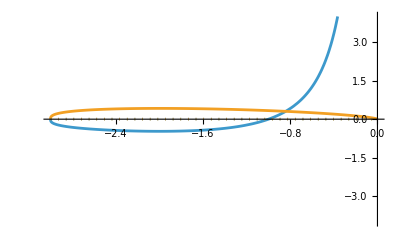

```mathematica
ReImPlot[{-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3)),-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3)}, {t1,-3,0},
PlotRange->{Automatic, {-4, 4}}
]
```

```mathematica
-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3))/.{t1->-2}//N
```

-0.47247

```mathematica
tudata = Table[{-2+Sqrt[1+12 m (u/.First[uvals[m]])^2], u/.First[uvals[m]]}, {m, -3/(4 2^(2/3)), 10, .01}];
```

```mathematica
tudatareal = Select[tudata, FreeQ[#,Complex]&];
```

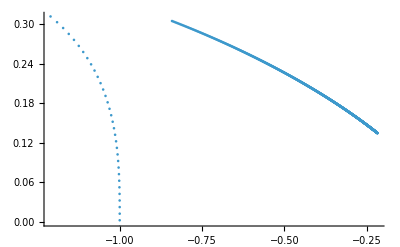

```mathematica
ListPlot[tudatareal]
```

```mathematica
bTot1
```

{b→(t1-√6 √X0)/(t1+√6 √X0)}

```mathematica
First[u/.uvals[1.]]//N
{Sqrt[t1sq],-2+Sqrt[1+12m u^2], 3(4m u^2+18u^3-1)/(12m u^2+1)}/.{m->1,u->%}
t1^2/2+t1/.{t1->Last[%]}
```

0.263185

{0.646782,-0.646782,-0.646782}

-0.437619

```mathematica
First[u/.uvals[1.]]//N
X0/.X0tot1/.{m->1,u->%}/.{t1->-0.6467824154242932}
```

0.263185

-0.437619

```mathematica
With[{m=N[2,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]];
A1/.{b->%}/.BWEval
```

u = 0.227203634857985759161254765346706290384

b = -0.79822170716314772598004515101171238668+0.60236376568776946837965610457745714968 ⅈ

1.13841093952205567492550624228156048

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]]
B/.{b->%}/.Li2Eval
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

-0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

0.523598775598298873077107230546583814+1.15732210074666531243235075733319062 ⅈ

```mathematica
N[Pi/6,40]
```

0.5235987755982988730771072305465838140329

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
Chop@Limit[pxy2/.u->u0, z->0]
]]
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

{1.4902161200999536481163868423786267429,0.81917251339616443969957118834242704035}

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]];
{{1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)}}/.{b->%}
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

{{1.490216120099953648116386842378626743+0. ⅈ,0.81917251339616443969957118834242704035+0. ⅈ}}

## Further Numerical checks

```mathematica
mvals=RandomComplex[{-20-20I,20+20I}, 10^5];
```

```mathematica
(*uv = u/.First[uvals[#]]&/@mvals;*)
```

```mathematica
TakeSmallest[{1,2,3}, 1]
```

{1}

```mathematica
RandomComplex[{-20-20I,20+20I}, 1]//AbsoluteTiming
```

{0.00002,{-3.81769-1.71869 ⅈ}}

```mathematica
(First@SortBy[u/.NSolve[delt[#,u]==0,u], Abs])&/@mvals;
```

$Aborted

```mathematica
t1vals=MapThread[-2+Sqrt[1+12#1 #2^2]&, {mvals,uv}];
```

```mathematica
(*ComplexListPlot[mvals]*)
```

```mathematica
(*ComplexListPlot[uv]*)
```

```mathematica
(*ComplexListPlot[t1vals]*)
```

```mathematica
sol100 = Simplify[Solve[delt[m,u]==0,u]];
```

```mathematica
ParametricPlot[ReIm[u/.sol100/.m->N[1,50]Exp[I th]], {th, -Pi,Pi},
PlotPoints->200,
MaxRecursion->5
]
```

```mathematica
mvals=KroneckerProduct[N[Range[2,10,1],50],Exp[I RandomReal[{-Pi,Pi}, 100]]];
```

```mathematica
mvals=N[1,50]Exp[I RandomReal[{-Pi,Pi}, 4000]];
```

```mathematica
uv=Map[u/.NSolve[delt[#,u]==0,u]&, mvals,{-1}];
umin=Table[First@SortBy[u, Abs], {u, uv}];
```

```mathematica
uv//Dimensions
```

{4000,4}

```mathematica
ComplexListPlot[Flatten[mvals],
PlotRange->{{-4,4},{-4,4}},
Epilog->{PointSize[.02],Point[{{3/(8 2^(2/3)),(3 √3)/(8 2^(2/3))},{-3/2^(2/3),(3 √3)/2^(2/3)},{3 2^(1/3),0},{-3/2^(2/3),-(3 √3)/2^(2/3)},{-3/(4 2^(2/3)),0},{3/(8 2^(2/3)),-(3 √3)/(8 2^(2/3))}}]}
]
```

```mathematica
ComplexListPlot[umin]
```

```mathematica
ComplexListPlot[{Flatten[uv],umin},
PlotRange->{{-4,4},{-4,4}},
PlotStyle->{Automatic, Directive[PointSize[.01]]},
Epilog->{Black,PointSize[.01],Point[{{-1/(3 2^(2/3)),-1/(2^(2/3) √3)},{1/(6 2^(2/3)),-1/(2 2^(2/3) √3)},{-1/(3 2^(2/3)),0},{1/(6 2^(2/3)),1/(2 2^(2/3) √3)},{2^(1/3)/3,0},{-1/(3 2^(2/3)),1/(2^(2/3) √3)}}]}
]
```

```mathematica
NSolve[delt[1,u]==0,u]
```

{{u→-3.02572},{u→-0.255099-0.221553 ⅈ},{u→-0.255099+0.221553 ⅈ},{u→0.263185}}

```mathematica
thGrid=Range[-Pi,Pi,.02];
rGrid=Range[0.1,10,.07];
mvals=Flatten@KroneckerProduct[rGrid,Exp[I thGrid]];
uv=Map[u/.NSolve[delt[#,u]==0,u]&, mvals,{-1}];
umin=Table[First@SortBy[u, Abs], {u, uv}];
t1vals=MapThread[-2+Sqrt[1+12#1 #2^2]&, {mvals,umin}];
```

```mathematica
ComplexListPlot[mvals,PlotRange->Full]
```

```mathematica
ComplexListPlot[umin]
```

```mathematica
ComplexListPlot[t1vals
]
```

```mathematica
ComplexListPlot[umin,
PlotRange->Full
]
```

## Check Marcos

```mathematica
MirrorCurve[x,y,m,u]//Expand
```

-1/u+m/x+x+1/(x y)+y

```mathematica
1+X+Y+z[1]/X+(z[1] z[2])/(X Y)/.{z[1]->m/ut^2,z[2]->1/m/ut};
ut^3*%//Expand
```

ut^3+(m ut)/X+ut^3 X+1/(X Y)+ut^3 Y

```mathematica
1+X+Y+z[1]/X+(z[1] z[2])/(X Y)
%/.{z[1]->m u^2,z[2]->u/m}
%/u^3//Expand
```

1+X+Y+z[1]/X+(z[1] z[2])/(X Y)

1+(m u^2)/X+X+u^3/(X Y)+Y

1/u^3+m/(u X)+X/u^3+1/(X Y)+Y/u^3

```mathematica
(x^2 y + x y^2 + x y + z1 y + z2 x^2)/(x y)//Expand
```

1+x+y+z1/x+(x z2)/y

```mathematica
(1+X+Y+z[1]/X+(z[1] z[2])/(X Y))X Y//Expand
```

X Y+X^2 Y+X Y^2+Y z[1]+z[1] z[2]